# Aula 7 - Análise de parâmetros e avaliação das soluções

## Funções auxiliares

```mathematica
MOPerceptron[x_List,W_List,b_List,f_List]:=With[{L=Length[W]},Table[f⟦i⟧[Dot[W⟦i⟧,x]+b⟦i⟧],{i,1,L}]];
```

```mathematica
TrainMOPerceptron[inputs_List,outputs_List,f_List,maxit_Integer,eps_,alpha_]:=
Module[{W=Table[RandomReal[{-0.1,0.1}],Length[outputs⟦1⟧],Length[inputs⟦1⟧]],B=Table[RandomReal[{-0.1,0.1}],Length[outputs⟦1⟧]],i=1,e=Infinity},
While[i≤maxit&&e>eps,
e=0;
For[j=1,j≤Length[inputs],j++,
With[{ej=(outputs⟦j⟧-MOPerceptron[inputs⟦j⟧,W,B,f])},
W=W+alpha*Dot[Transpose[{ej}],{inputs⟦j⟧}];
B=B+alpha*ej;
e=e+Total[ej^2]/Length[ej];
];
];
e=e/Length[inputs];
i++;
];
{W,B,i-1,e}
]
```

```mathematica
TestMOPerceptron[inputs_List,outputs_List,W_List,b_List,f_List,roundingf_,fullreport_:False]:=Module[{y=roundingf[ #]&/@Table[MOPerceptron[x,W,b,f],{x,inputs}],acc=0},
acc=N[Total[Table[If[outputs⟦i⟧==y⟦i⟧,1,0],{i,1,Length[outputs]}]]/Length[outputs]];
If[fullreport,
{acc,Table[{y⟦i⟧,outputs⟦i⟧,If[y⟦i⟧==outputs⟦i⟧,1,0]},{i,1,Length[outputs]}]}
,
acc
]
];
```

```mathematica
LogisticF[x_,lambda_:1]:=1/(1+Exp[-lambda*x]);
```

```mathematica
KFoldsTestMOPerceptron[foldsInputs_,foldsOutputs_,f_List,maxit_Integer,eps_,alpha_,roundingf_]:=Module[{traindata={Flatten[Drop[foldsInputs,{#}],1],Flatten[Drop[foldsOutputs,{#}],1]}&/@Range[1,Length[foldsInputs]],testdata={foldsInputs⟦#⟧,foldsOutputs⟦#⟧}&/@Range[1,Length[foldsInputs]],trainednets},
trainednets=Table[TrainMOPerceptron[traindata⟦i,1⟧,traindata⟦i,2⟧,f,maxit,eps,alpha]⟦{1,2}⟧,{i,1,Length[traindata]}];
Table[TestMOPerceptron[testdata⟦i,1⟧,testdata⟦i,2⟧,trainednets⟦i,1⟧,trainednets⟦i,2⟧,f,roundingf,False],{i,1,Length[foldsInputs]}]
];
```

```mathematica
HighestValueRounding[x_]:=With[{maxpos=First@Flatten@Position[x,Max[x]]},Table[If[i==maxpos,1,0],{i,1,Length[x]}]];
```

```mathematica
RouletteSelection[pool_,fitness_,n_]:=With[{p=fitness/Total[fitness]},RandomChoice[p-> pool,n]];
```

```mathematica
AG[pop_List,fFun_,cFun_,mFun_,pm_,maxit_Integer,fGoal_:Infinity,sType_:All,showHistory_:False]:=
Module[{population=pop,popfitness=fFun[#]&/@pop,offspring={},offfitness,L=Length[pop],history={},i=1},
history=Join[history,{{MapThread[List,{population,popfitness}],Max[popfitness],Mean[popfitness]}}];
While[i≤maxit&&Max[popfitness]<fGoal,
offspring=mFun[cFun[population],pm];
offfitness=fFun[#]&/@offspring;
If[sType==All,
population=RouletteSelection[Join[population,offspring],Join[popfitness,offfitness],L],
population=RouletteSelection[offspring,offfitness,L]
];
popfitness=fFun[#]&/@population;
history=Join[history,{{MapThread[List,{population,popfitness}],Max[popfitness],Mean[popfitness]}}];
i++;
];
With[{M=Max[popfitness]},
If[!showHistory,
{MapThread[List,{population,popfitness}],M,Mean[popfitness]},
history
]
]
];
```

```mathematica
FitnessReport[historico_]:=Transpose[{#⟦2⟧,#⟦3⟧}&/@historico];
```

```mathematica
BestReport[historico_]:=Table[g⟦1⟧⟦First[Flatten[Position[g⟦2⟧,Max[g⟦2⟧]]]]⟧,{g,Transpose[#⟦1⟧]&/@historico}];
```

```mathematica
CompetitiveTraining[inputs_List,N_,maxit_Integer,alpha_]:=Module[{W=Table[RandomReal[{-0.1,0.1}],N,Length[inputs⟦1⟧]],i=1},
While[i≤maxit,
For[j=1,j≤Length[inputs],j++,
With[{dists=Norm[#]&/@Table[inputs⟦j⟧-W⟦k⟧,{k,1,N}]},
With[{pos=Flatten[Position[dists,Min[dists]]]⟦1⟧},
W⟦pos⟧+=alpha*(inputs⟦j⟧-W⟦pos⟧)
];
];
];
i++
];
W
];
```

```mathematica
ClosestCentroid[centroids_,example_]:=First[SortBy[centroids,EuclideanDistance[#,example]&]];
```

```mathematica
Clustering[centroids_,data_]:=Map[First,GatherBy[{#,ClosestCentroid[centroids,#]}&/@data,Last],{2}];
```

## Datasets

### Iris

#### Dados

(comprimento_sepala, largura_sepala, comprimento_petala, largura_petala, classe);
medidas em centímetros
classes: Iris setosa; Iris versicolor; Iris virginica

```mathematica
irisdata={{5.1,3.5,1.4,0.2,"Iris-setosa"},{4.9,3.,1.4,0.2,"Iris-setosa"},{4.7,3.2,1.3,0.2,"Iris-setosa"},{4.6,3.1,1.5,0.2,"Iris-setosa"},{5.,3.6,1.4,0.2,"Iris-setosa"},{5.4,3.9,1.7,0.4,"Iris-setosa"},{4.6,3.4,1.4,0.3,"Iris-setosa"},{5.,3.4,1.5,0.2,"Iris-setosa"},{4.4,2.9,1.4,0.2,"Iris-setosa"},{4.9,3.1,1.5,0.1,"Iris-setosa"},{5.4,3.7,1.5,0.2,"Iris-setosa"},{4.8,3.4,1.6,0.2,"Iris-setosa"},{4.8,3.,1.4,0.1,"Iris-setosa"},{4.3,3.,1.1,0.1,"Iris-setosa"},{5.8,4.,1.2,0.2,"Iris-setosa"},{5.7,4.4,1.5,0.4,"Iris-setosa"},{5.4,3.9,1.3,0.4,"Iris-setosa"},{5.1,3.5,1.4,0.3,"Iris-setosa"},{5.7,3.8,1.7,0.3,"Iris-setosa"},{5.1,3.8,1.5,0.3,"Iris-setosa"},{5.4,3.4,1.7,0.2,"Iris-setosa"},{5.1,3.7,1.5,0.4,"Iris-setosa"},{4.6,3.6,1.,0.2,"Iris-setosa"},{5.1,3.3,1.7,0.5,"Iris-setosa"},{4.8,3.4,1.9,0.2,"Iris-setosa"},{5.,3.,1.6,0.2,"Iris-setosa"},{5.,3.4,1.6,0.4,"Iris-setosa"},{5.2,3.5,1.5,0.2,"Iris-setosa"},{5.2,3.4,1.4,0.2,"Iris-setosa"},{4.7,3.2,1.6,0.2,"Iris-setosa"},{4.8,3.1,1.6,0.2,"Iris-setosa"},{5.4,3.4,1.5,0.4,"Iris-setosa"},{5.2,4.1,1.5,0.1,"Iris-setosa"},{5.5,4.2,1.4,0.2,"Iris-setosa"},{4.9,3.1,1.5,0.1,"Iris-setosa"},{5.,3.2,1.2,0.2,"Iris-setosa"},{5.5,3.5,1.3,0.2,"Iris-setosa"},{4.9,3.1,1.5,0.1,"Iris-setosa"},{4.4,3.,1.3,0.2,"Iris-setosa"},{5.1,3.4,1.5,0.2,"Iris-setosa"},{5.,3.5,1.3,0.3,"Iris-setosa"},{4.5,2.3,1.3,0.3,"Iris-setosa"},{4.4,3.2,1.3,0.2,"Iris-setosa"},{5.,3.5,1.6,0.6,"Iris-setosa"},{5.1,3.8,1.9,0.4,"Iris-setosa"},{4.8,3.,1.4,0.3,"Iris-setosa"},{5.1,3.8,1.6,0.2,"Iris-setosa"},{4.6,3.2,1.4,0.2,"Iris-setosa"},{5.3,3.7,1.5,0.2,"Iris-setosa"},{5.,3.3,1.4,0.2,"Iris-setosa"},{7.,3.2,4.7,1.4,"Iris-versicolor"},{6.4,3.2,4.5,1.5,"Iris-versicolor"},{6.9,3.1,4.9,1.5,"Iris-versicolor"},{5.5,2.3,4.,1.3,"Iris-versicolor"},{6.5,2.8,4.6,1.5,"Iris-versicolor"},{5.7,2.8,4.5,1.3,"Iris-versicolor"},{6.3,3.3,4.7,1.6,"Iris-versicolor"},{4.9,2.4,3.3,1.,"Iris-versicolor"},{6.6,2.9,4.6,1.3,"Iris-versicolor"},{5.2,2.7,3.9,1.4,"Iris-versicolor"},{5.,2.,3.5,1.,"Iris-versicolor"},{5.9,3.,4.2,1.5,"Iris-versicolor"},{6.,2.2,4.,1.,"Iris-versicolor"},{6.1,2.9,4.7,1.4,"Iris-versicolor"},{5.6,2.9,3.6,1.3,"Iris-versicolor"},{6.7,3.1,4.4,1.4,"Iris-versicolor"},{5.6,3.,4.5,1.5,"Iris-versicolor"},{5.8,2.7,4.1,1.,"Iris-versicolor"},{6.2,2.2,4.5,1.5,"Iris-versicolor"},{5.6,2.5,3.9,1.1,"Iris-versicolor"},{5.9,3.2,4.8,1.8,"Iris-versicolor"},{6.1,2.8,4.,1.3,"Iris-versicolor"},{6.3,2.5,4.9,1.5,"Iris-versicolor"},{6.1,2.8,4.7,1.2,"Iris-versicolor"},{6.4,2.9,4.3,1.3,"Iris-versicolor"},{6.6,3.,4.4,1.4,"Iris-versicolor"},{6.8,2.8,4.8,1.4,"Iris-versicolor"},{6.7,3.,5.,1.7,"Iris-versicolor"},{6.,2.9,4.5,1.5,"Iris-versicolor"},{5.7,2.6,3.5,1.,"Iris-versicolor"},{5.5,2.4,3.8,1.1,"Iris-versicolor"},{5.5,2.4,3.7,1.,"Iris-versicolor"},{5.8,2.7,3.9,1.2,"Iris-versicolor"},{6.,2.7,5.1,1.6,"Iris-versicolor"},{5.4,3.,4.5,1.5,"Iris-versicolor"},{6.,3.4,4.5,1.6,"Iris-versicolor"},{6.7,3.1,4.7,1.5,"Iris-versicolor"},{6.3,2.3,4.4,1.3,"Iris-versicolor"},{5.6,3.,4.1,1.3,"Iris-versicolor"},{5.5,2.5,4.,1.3,"Iris-versicolor"},{5.5,2.6,4.4,1.2,"Iris-versicolor"},{6.1,3.,4.6,1.4,"Iris-versicolor"},{5.8,2.6,4.,1.2,"Iris-versicolor"},{5.,2.3,3.3,1.,"Iris-versicolor"},{5.6,2.7,4.2,1.3,"Iris-versicolor"},{5.7,3.,4.2,1.2,"Iris-versicolor"},{5.7,2.9,4.2,1.3,"Iris-versicolor"},{6.2,2.9,4.3,1.3,"Iris-versicolor"},{5.1,2.5,3.,1.1,"Iris-versicolor"},{5.7,2.8,4.1,1.3,"Iris-versicolor"},{6.3,3.3,6.,2.5,"Iris-virginica"},{5.8,2.7,5.1,1.9,"Iris-virginica"},{7.1,3.,5.9,2.1,"Iris-virginica"},{6.3,2.9,5.6,1.8,"Iris-virginica"},{6.5,3.,5.8,2.2,"Iris-virginica"},{7.6,3.,6.6,2.1,"Iris-virginica"},{4.9,2.5,4.5,1.7,"Iris-virginica"},{7.3,2.9,6.3,1.8,"Iris-virginica"},{6.7,2.5,5.8,1.8,"Iris-virginica"},{7.2,3.6,6.1,2.5,"Iris-virginica"},{6.5,3.2,5.1,2.,"Iris-virginica"},{6.4,2.7,5.3,1.9,"Iris-virginica"},{6.8,3.,5.5,2.1,"Iris-virginica"},{5.7,2.5,5.,2.,"Iris-virginica"},{5.8,2.8,5.1,2.4,"Iris-virginica"},{6.4,3.2,5.3,2.3,"Iris-virginica"},{6.5,3.,5.5,1.8,"Iris-virginica"},{7.7,3.8,6.7,2.2,"Iris-virginica"},{7.7,2.6,6.9,2.3,"Iris-virginica"},{6.,2.2,5.,1.5,"Iris-virginica"},{6.9,3.2,5.7,2.3,"Iris-virginica"},{5.6,2.8,4.9,2.,"Iris-virginica"},{7.7,2.8,6.7,2.,"Iris-virginica"},{6.3,2.7,4.9,1.8,"Iris-virginica"},{6.7,3.3,5.7,2.1,"Iris-virginica"},{7.2,3.2,6.,1.8,"Iris-virginica"},{6.2,2.8,4.8,1.8,"Iris-virginica"},{6.1,3.,4.9,1.8,"Iris-virginica"},{6.4,2.8,5.6,2.1,"Iris-virginica"},{7.2,3.,5.8,1.6,"Iris-virginica"},{7.4,2.8,6.1,1.9,"Iris-virginica"},{7.9,3.8,6.4,2.,"Iris-virginica"},{6.4,2.8,5.6,2.2,"Iris-virginica"},{6.3,2.8,5.1,1.5,"Iris-virginica"},{6.1,2.6,5.6,1.4,"Iris-virginica"},{7.7,3.,6.1,2.3,"Iris-virginica"},{6.3,3.4,5.6,2.4,"Iris-virginica"},{6.4,3.1,5.5,1.8,"Iris-virginica"},{6.,3.,4.8,1.8,"Iris-virginica"},{6.9,3.1,5.4,2.1,"Iris-virginica"},{6.7,3.1,5.6,2.4,"Iris-virginica"},{6.9,3.1,5.1,2.3,"Iris-virginica"},{5.8,2.7,5.1,1.9,"Iris-virginica"},{6.8,3.2,5.9,2.3,"Iris-virginica"},{6.7,3.3,5.7,2.5,"Iris-virginica"},{6.7,3.,5.2,2.3,"Iris-virginica"},{6.3,2.5,5.,1.9,"Iris-virginica"},{6.5,3.,5.2,2.,"Iris-virginica"},{6.2,3.4,5.4,2.3,"Iris-virginica"},{5.9,3.,5.1,1.8,"Iris-virginica"}};
```

## Exemplo 1: Classificação do dataset Iris utilizando um perceptron de três saídas

Iris setosa: (1,0,0); Iris versicolor: (0,1,0); Iris virginica: (0,0,1)

```mathematica
Ex1Entradas=#⟦1;;4⟧&/@irisdata;
```

```mathematica
Ex1Saidas=(#⟦5⟧&/@irisdata)/.{"Iris-setosa"->{1,0,0},"Iris-versicolor"->{0,1,0},"Iris-virginica"->{0,0,1}};
```

```mathematica
treinamentosEx1=Table[{lambda,alpha,TrainMOPerceptron[Ex1Entradas,Ex1Saidas,Table[LogisticF[#,lambda]&,3],500,0,alpha]},{lambda,Range[0.8,1.2,0.1]},{alpha,Range[0.1,0.3,0.05]}];
```

```mathematica
Join[{{"Lambda","Alpha","Error"}},SortBy[Flatten[Table[Flatten[{#⟦{1,2}⟧,#⟦-1,-1⟧}]&/@t,{t,treinamentosEx1}],1],Last]]//MatrixForm
```

(Lambda | Alpha | Error
1.2 | 0.1 | 0.0122988
0.8 | 0.15 | 0.0123038
1.1 | 0.1 | 0.0123051
1. | 0.1 | 0.0124141
0.9 | 0.15 | 0.0124818
0.9 | 0.1 | 0.0126552
1. | 0.15 | 0.0129258
0.8 | 0.1 | 0.0130175
0.8 | 0.2 | 0.0133198
1.1 | 0.15 | 0.0135364
1.2 | 0.15 | 0.0140991
0.9 | 0.2 | 0.0141069
1. | 0.2 | 0.0146914
0.8 | 0.25 | 0.0146942
1.1 | 0.2 | 0.0151634
0.8 | 0.3 | 0.0153052
0.9 | 0.25 | 0.0153464
1.2 | 0.2 | 0.0156275
1. | 0.25 | 0.0156339
0.9 | 0.3 | 0.0161974
1. | 0.3 | 0.0168994
1.1 | 0.25 | 0.0178652
1.2 | 0.25 | 0.0181563
1.2 | 0.3 | 0.0205184
1.1 | 0.3 | 0.0210843)

```mathematica
Ex1BestLambda=SortBy[Flatten[Table[Flatten[{#⟦{1,2}⟧,#⟦-1,-1⟧}]&/@t,{t,treinamentosEx1}],1],Last]⟦1,1⟧
Ex1BestAlpha=SortBy[Flatten[Table[Flatten[{#⟦{1,2}⟧,#⟦-1,-1⟧}]&/@t,{t,treinamentosEx1}],1],Last]⟦1,2⟧
```

1.2

0.1

```mathematica
{Ex1BestW,Ex1BestB}=Select[Flatten[treinamentosEx1,1],((#⟦1⟧==Ex1BestLambda)&&(#⟦2⟧==Ex1BestAlpha))&]⟦1,3,{1,2}⟧
```

{{{0.872166,3.21002,-5.01098,-2.28336},{6.80311,-6.60659,-0.694093,-11.2812},{-7.1161,-7.56574,10.1608,16.538}},{0.682672,-10.2238,-7.83022}}

```mathematica
TestMOPerceptron[Ex1Entradas,Ex1Saidas,Ex1BestW,Ex1BestB,Table[LogisticF[#,Ex1BestLambda]&,3],HighestValueRounding,False]
```

0.82

Rankeando os pares de parâmetro de acordo com a acurácia, e não com o erro:

```mathematica
Table[{t⟦1⟧,t⟦2⟧,TestMOPerceptron[Ex1Entradas,Ex1Saidas,t⟦3,1⟧,t⟦3,2⟧,Table[LogisticF[#,Ex1BestLambda]&,3],HighestValueRounding,False]},{t,Flatten[treinamentosEx1,1]}]//MatrixForm
```

(0.8 | 0.1 | 0.826667
0.8 | 0.15 | 0.82
0.8 | 0.2 | 0.813333
0.8 | 0.25 | 0.8
0.8 | 0.3 | 0.806667
0.9 | 0.1 | 0.826667
0.9 | 0.15 | 0.82
0.9 | 0.2 | 0.813333
0.9 | 0.25 | 0.806667
0.9 | 0.3 | 0.806667
1. | 0.1 | 0.826667
1. | 0.15 | 0.813333
1. | 0.2 | 0.806667
1. | 0.25 | 0.806667
1. | 0.3 | 0.806667
1.1 | 0.1 | 0.826667
1.1 | 0.15 | 0.813333
1.1 | 0.2 | 0.806667
1.1 | 0.25 | 0.806667
1.1 | 0.3 | 0.78
1.2 | 0.1 | 0.82
1.2 | 0.15 | 0.813333
1.2 | 0.2 | 0.806667
1.2 | 0.25 | 0.8
1.2 | 0.3 | 0.766667)

Fazendo a validação em 10-pastas para os dados fornecidos

Escolhendo os valores de alpha e lambda:

```mathematica
foldsEx1alpha=0.1;
foldsEx1lambda=0.8;
```

Randomizando a ordem dos dados:

```mathematica
ordemEx1=RandomSample[Range[1,Length[Ex1Entradas]],Length[Ex1Entradas]]
```

{20,119,96,72,75,51,49,106,104,55,147,133,149,4,46,10,69,78,32,137,54,59,48,35,33,83,99,41,37,135,79,19,97,95,102,90,64,60,5,142,8,93,56,30,100,115,6,50,40,98,38,109,73,125,61,87,103,14,34,120,140,62,65,86,130,63,105,53,94,28,57,118,47,2,77,122,117,13,150,121,18,70,16,52,71,42,134,43,91,123,1,7,146,131,31,15,44,27,81,36,88,67,66,114,124,128,89,85,113,84,21,26,138,139,45,80,110,9,108,23,129,17,92,39,111,29,74,132,3,25,82,136,148,127,141,144,76,116,12,143,145,22,11,101,107,24,58,126,68,112}

Dividindo os dados em pastas:

```mathematica
foldsEx1Entradas=Partition[Ex1Entradas⟦ordemEx1⟧,10];
foldsEx1Saidas=Partition[Ex1Saidas⟦ordemEx1⟧,10];
```

Testando os modelos treinados em pastas

```mathematica
foldsResultsEx1=KFoldsTestMOPerceptron[foldsEx1Entradas,foldsEx1Saidas,Table[LogisticF[#,foldsEx1lambda]&,3],500,0,foldsEx1alpha,HighestValueRounding]
```

{1.,0.8,1.,0.8,1.,0.9,0.9,0.9,0.9,1.,0.7,1.,1.,1.,1.}

```mathematica
{Mean[foldsResultsEx1],StandardDeviation[foldsResultsEx1]}
```

{0.926667,0.096115}

## Exemplo 2: Exemplo 1 mas com a ordem dos dados randomizada

Iris setosa: (1,0,0); Iris versicolor: (0,1,0); Iris virginica: (0,0,1)

```mathematica
Ex2ordem=RandomSample[Range[1,Length[Ex1Entradas]],Length[Ex1Entradas]];
```

```mathematica
Ex2Entradas=(#⟦1;;4⟧&/@irisdata)⟦Ex2ordem⟧;
```

Part::pkspec1: The expression Ex2ordem cannot be used as a part specification.

```mathematica
Ex2Saidas=((#⟦5⟧&/@irisdata)/.{"Iris-setosa"->{1,0,0},"Iris-versicolor"->{0,1,0},"Iris-virginica"->{0,0,1}})⟦Ex2ordem⟧;
```

Part::pkspec1: The expression Ex2ordem cannot be used as a part specification.

```mathematica
treinamentosEx2=Table[{lambda,alpha,TrainMOPerceptron[Ex2Entradas,Ex2Saidas,Table[LogisticF[#,lambda]&,3],500,0,alpha]},{lambda,Range[0.8,1.2,0.1]},{alpha,Range[0.1,0.3,0.05]}];
```

```mathematica
Join[{{"Lambda","Alpha","Error"}},SortBy[Flatten[Table[Flatten[{#⟦{1,2}⟧,#⟦-1,-1⟧}]&/@t,{t,treinamentosEx2}],1],Last]]//MatrixForm
```

(Lambda | Alpha | Error
0.8 | 0.1 | 0.0928869
0.9 | 0.1 | 0.0949573
1. | 0.1 | 0.0967411
1.1 | 0.1 | 0.09828
1.2 | 0.1 | 0.0996897
0.8 | 0.15 | 0.0996904
0.9 | 0.15 | 0.101738
1. | 0.15 | 0.103756
0.8 | 0.2 | 0.104915
1.1 | 0.15 | 0.105125
1. | 0.2 | 0.107491
1.1 | 0.2 | 0.108427
0.9 | 0.2 | 0.108837
1.1 | 0.25 | 0.108958
1.2 | 0.15 | 0.109001
0.8 | 0.25 | 0.110228
0.8 | 0.3 | 0.111626
0.9 | 0.25 | 0.111914
1.2 | 0.25 | 0.113266
1.2 | 0.2 | 0.114086
0.9 | 0.3 | 0.114397
1. | 0.25 | 0.114789
1.2 | 0.3 | 0.114996
1. | 0.3 | 0.115948
1.1 | 0.3 | 0.120107)

```mathematica
Ex2BestLambda=SortBy[Flatten[Table[Flatten[{#⟦{1,2}⟧,#⟦-1,-1⟧}]&/@t,{t,treinamentosEx2}],1],Last]⟦1,1⟧
Ex2BestAlpha=SortBy[Flatten[Table[Flatten[{#⟦{1,2}⟧,#⟦-1,-1⟧}]&/@t,{t,treinamentosEx2}],1],Last]⟦1,2⟧
```

0.8

0.1

```mathematica
{Ex2BestW,Ex2BestB}=Select[Flatten[treinamentosEx2,1],((#⟦1⟧==Ex2BestLambda)&&(#⟦2⟧==Ex2BestAlpha))&]⟦1,3,{1,2}⟧
```

{{{1.25697,4.59965,-7.03975,-3.42677},{-0.144471,-6.98728,1.96288,-5.59977},{-9.72117,-9.77349,14.7448,20.3231}},{0.766484,16.015,-16.9335}}

```mathematica
TestMOPerceptron[Ex2Entradas,Ex2Saidas,Ex2BestW,Ex2BestB,Table[LogisticF[#,Ex2BestLambda]&,3],HighestValueRounding,False]
```

0.96

Rankeando os pares de parâmetro de acordo com a acurácia, e não com o erro:

```mathematica
Table[{t⟦1⟧,t⟦2⟧,TestMOPerceptron[Ex2Entradas,Ex2Saidas,t⟦3,1⟧,t⟦3,2⟧,Table[LogisticF[#,Ex2BestLambda]&,3],HighestValueRounding,False]},{t,Flatten[treinamentosEx2,1]}]//MatrixForm
```

(0.8 | 0.1 | 0.96
0.8 | 0.15 | 0.96
0.8 | 0.2 | 0.966667
0.8 | 0.25 | 0.946667
0.8 | 0.3 | 0.946667
0.9 | 0.1 | 0.96
0.9 | 0.15 | 0.96
0.9 | 0.2 | 0.953333
0.9 | 0.25 | 0.94
0.9 | 0.3 | 0.94
1. | 0.1 | 0.96
1. | 0.15 | 0.96
1. | 0.2 | 0.96
1. | 0.25 | 0.933333
1. | 0.3 | 0.966667
1.1 | 0.1 | 0.96
1.1 | 0.15 | 0.966667
1.1 | 0.2 | 0.953333
1.1 | 0.25 | 0.94
1.1 | 0.3 | 0.96
1.2 | 0.1 | 0.96
1.2 | 0.15 | 0.953333
1.2 | 0.2 | 0.933333
1.2 | 0.25 | 0.92
1.2 | 0.3 | 0.933333)

Fazendo a validação em 10-pastas para os dados fornecidos

Escolhendo os valores de alpha e lambda:

```mathematica
foldsEx2alpha=0.2;
foldsEx2lambda=0.8;
```

Dividindo os dados em pastas:

```mathematica
foldsEx2Entradas=Partition[Ex2Entradas,10];
foldsEx2Saidas=Partition[Ex2Saidas,10];
```

Testando os modelos treinados em pastas

```mathematica
foldsResultsEx2=KFoldsTestMOPerceptron[foldsEx2Entradas,foldsEx2Saidas,Table[LogisticF[#,foldsEx2lambda]&,3],500,0,foldsEx1alpha,HighestValueRounding]
```

{1.,1.,1.,1.,0.9,0.9,1.,0.8,1.,1.,0.9,1.,1.,0.9,1.}

```mathematica
{Mean[foldsResultsEx1],StandardDeviation[foldsResultsEx1]}
```

{0.926667,0.096115}

## Exemplo 3: Matriz de Confusão do melhor modelo do Exemplo 2

```mathematica
Ex3treinamento=TrainMOPerceptron[Ex2Entradas,Ex2Saidas,Table[LogisticF[#,foldsEx2lambda]&,3],500,0,foldsEx2alpha];
```

```mathematica
Ex3results=TestMOPerceptron[Ex2Entradas,Ex2Saidas,Ex3treinamento⟦1⟧,Ex3treinamento⟦2⟧,Table[LogisticF[#,Ex2BestLambda]&,3],HighestValueRounding,True]
```

{0.966667,{{{0,0,1},{0,0,1},1},{{0,0,1},{0,0,1},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{0,1,0},{0,1,0},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,1,0},0},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,1,0},0},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{0,0,1},{0,1,0},0},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,1,0},0},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{0,1,0},{0,1,0},1},{{0,1,0},{0,1,0},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,1,0},0},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{0,1,0},{0,1,0},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1},{{1,0,0},{1,0,0},1},{{0,0,1},{0,0,1},1},{{0,0,1},{0,0,1},1},{{1,0,0},{1,0,0},1}}}

```mathematica
Ex3results⟦2⟧/.{{1,0,0}->1,{0,1,0}->2,{0,0,1}->3}
```

{{3,3,1},{3,3,1},{3,3,1},{2,2,1},{3,3,1},{2,2,1},{3,3,1},{1,1,1},{1,1,1},{1,1,1},{3,3,1},{2,2,1},{3,3,1},{1,1,1},{1,1,1},{2,2,1},{3,3,1},{1,1,1},{2,2,1},{3,3,1},{1,1,1},{2,2,1},{1,1,1},{3,3,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{2,2,1},{1,1,1},{1,1,1},{2,2,1},{2,2,1},{3,3,1},{3,3,1},{1,1,1},{2,2,1},{3,3,1},{3,3,1},{1,1,1},{1,1,1},{2,2,1},{1,1,1},{2,2,1},{1,1,1},{3,3,1},{2,2,1},{1,1,1},{2,2,1},{2,2,1},{2,2,1},{1,1,1},{3,2,0},{3,3,1},{2,2,1},{2,2,1},{3,3,1},{3,3,1},{1,1,1},{1,1,1},{3,3,1},{3,3,1},{2,2,1},{3,3,1},{2,2,1},{2,2,1},{3,3,1},{1,1,1},{2,2,1},{2,2,1},{3,3,1},{2,2,1},{3,2,0},{2,2,1},{3,3,1},{3,2,0},{3,3,1},{1,1,1},{3,3,1},{1,1,1},{3,3,1},{3,3,1},{1,1,1},{3,3,1},{3,3,1},{2,2,1},{1,1,1},{2,2,1},{1,1,1},{3,3,1},{2,2,1},{3,3,1},{2,2,1},{3,3,1},{3,3,1},{2,2,1},{2,2,1},{1,1,1},{2,2,1},{1,1,1},{3,3,1},{1,1,1},{2,2,1},{2,2,1},{1,1,1},{1,1,1},{3,3,1},{2,2,1},{3,2,0},{3,3,1},{1,1,1},{3,3,1},{3,3,1},{1,1,1},{1,1,1},{3,3,1},{2,2,1},{1,1,1},{1,1,1},{3,3,1},{3,3,1},{2,2,1},{3,3,1},{2,2,1},{2,2,1},{3,3,1},{1,1,1},{2,2,1},{1,1,1},{2,2,1},{2,2,1},{2,2,1},{1,1,1},{1,1,1},{1,1,1},{3,2,0},{1,1,1},{3,3,1},{2,2,1},{3,3,1},{1,1,1},{3,3,1},{1,1,1},{2,2,1},{3,3,1},{1,1,1},{1,1,1},{3,3,1},{3,3,1},{1,1,1}}

Linhas: Previsto; Colunas: Real

```mathematica
Module[{matriz=Table[0,{i,1,3},{j,1,3}]},
((matriz⟦#⟦1⟧,#⟦2⟧⟧++)&/@(Ex3results⟦2⟧/.{{1,0,0}->1,{0,1,0}->2,{0,0,1}->3}));
matriz
]//MatrixForm
```

(50 | 0 | 0
0 | 45 | 0
0 | 5 | 50)

## Exemplo 4: Avaliação da quantidade de grupos em um problema de agrupamento utilizando redes neurais

### Cálculo de distâncias inter-grupos e intra-grupos

```mathematica
InterClusterDistance[c1_,c2_]:=Min[Flatten[Table[N@EuclideanDistance[x,y],{x,c1},{y,c2}]]];
IntraClusterDistance[c_]:=Mean[Flatten[Table[EuclideanDistance[c⟦i⟧,c⟦j⟧],{i,1,Length[c]-1},{j,i+1,Length[c]}]]/.{{}->{0}}];
```

```mathematica
InterClusterDistances[clusters_]:=Table[InterClusterDistance[clusters⟦i⟧,clusters⟦j⟧],{i,1,Length[clusters]-1},{j,i+1,Length[clusters]}];
IntraClusterDistances[clusters_]:=Table[IntraClusterDistance[c],{c,clusters}];
```

```mathematica
MeanInterClusterDistances[clusters_]:=Mean[Flatten@InterClusterDistances[clusters]];
MeanIntraClusterDistances[clusters_]:=Mean[IntraClusterDistances[clusters]];
```

```mathematica
Ex4Data=Flatten[{Table[{0.1+RandomReal[{-1.0,1.0}]/10,0.2+RandomReal[{-1.0,1.0}]/10},{20}],Table[{0.4+RandomReal[{-1.0,1.0}]/5,0.1+RandomReal[{-1.0,1.0}]/10},{100}],Table[{0.6+RandomReal[{-1.0,1.0}]/20,0.7+RandomReal[{-1.0,1.0}]/2},{50}],Table[{0.0+RandomReal[{-1.0,1.0}]/4,0.8+RandomReal[{-1.0,1.0}]/8},{30}],Table[{0.5+RandomReal[{-1.0,1.0}]/20,0.1+RandomReal[{-1.0,1.0}]/50},{20}]},1];
```

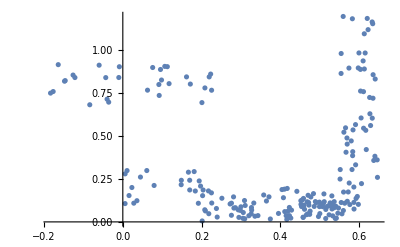

```mathematica
ListPlot[Ex4Data]
```

```mathematica
treinamentoEx4=Table[CompetitiveTraining[Ex4Data,n,100,0.1],{n,Range[2,7]}]
```

{{{0.0522334,0.845485},{0.505014,0.135046}},{{0.591055,0.397387},{0.476599,0.0957218},{0.0522334,0.845485}},{{0.476024,0.0959577},{0.0301415,0.842004},{0.606493,0.911307},{0.587104,0.376665}},{{0.596899,0.451414},{0.605798,0.932713},{0.495838,0.10256},{0.0301415,0.842004},{0.251448,0.0958681}},{{0.0301415,0.842004},{0.605798,0.932713},{0.153813,0.200327},{0.496133,0.102567},{0.596899,0.451414},{0.288688,0.0675637}},{{0.496133,0.102567},{0.153813,0.200327},{0.0301415,0.842004},{0.596899,0.451414},{0.288688,0.0675637},{0.605798,0.932713},{0.0100254,-0.0751566}}}

```mathematica
Ex4Clusterings=Clustering[#,Ex4Data]&/@treinamentoEx4;
```

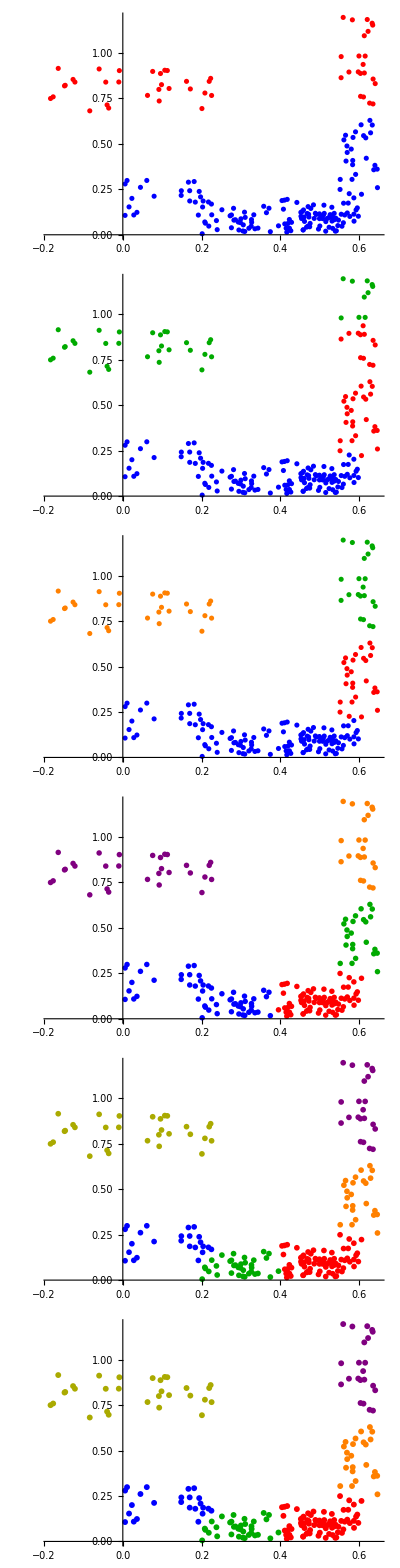

```mathematica
Transpose[{ListPlot[#,PlotStyle->{Blue,Red,Darker[Green],Orange,Purple,Darker[Yellow],Gray}⟦1;;Length[#]⟧]&/@Ex4Clusterings}]//Grid
```

```mathematica
Ex4Evaluations=MapThread[Join,{{{"||n = 2||"},{"||n = 3||"},{"||n = 4||"},{"||n = 5||"},{"||n = 6||"},{"||n = 7||"}},{MeanInterClusterDistances[#],MeanIntraClusterDistances[#]}&/@Ex4Clusterings}]//MatrixForm
```

(||n = 2|| | 0.090896 | 0.330692
||n = 3|| | 0.156287 | 0.272775
||n = 4|| | 0.292547 | 0.184052
||n = 5|| | 0.318491 | 0.15533
||n = 6|| | 0.327856 | 0.137402
||n = 7|| | 0.327856 | 0.137402)

### Testando diferentes valores de α para o melhor caso

```mathematica
treinamentoEx4Alpha=Table[CompetitiveTraining[Ex4Data,6,100,0.1],{alpha,Range[0.05,0.4,0.05]}]
```

{{{0.0301415,0.842004},{0.596899,0.451414},{0.495838,0.10256},{0.605798,0.932713},{0.251448,0.0958681},{0.0220382,-0.0900976}},{{-0.0594012,-0.0851201},{0.495838,0.10256},{0.605798,0.932713},{0.251448,0.0958681},{0.596899,0.451414},{0.0301415,0.842004}},{{0.288688,0.0675637},{0.0301415,0.842004},{0.596899,0.451414},{0.605798,0.932713},{0.496133,0.102567},{0.153813,0.200327}},{{0.596899,0.451414},{0.605798,0.932713},{-0.0897369,-0.095217},{0.495838,0.10256},{0.0301415,0.842004},{0.251448,0.0958681}},{{0.496133,0.102567},{0.0301415,0.842004},{0.288688,0.0675637},{0.153813,0.200327},{0.596899,0.451414},{0.605798,0.932713}},{{0.251448,0.0958681},{0.605798,0.932713},{0.0301415,0.842004},{0.028294,-0.092644},{0.495838,0.10256},{0.596899,0.451414}},{{0.153813,0.200327},{0.496133,0.102567},{0.0301415,0.842004},{0.288688,0.0675637},{0.605798,0.932713},{0.596899,0.451414}},{{0.288688,0.0675637},{0.605798,0.932713},{0.0301415,0.842004},{0.153813,0.200327},{0.496133,0.102567},{0.596899,0.451414}}}

```mathematica
Ex4ClusteringsAlpha=Clustering[#,Ex4Data]&/@treinamentoEx4Alpha;
```

```mathematica
Ex4EvaluationsAlpha=MapThread[Join,{{{"||α = 0.05||"},{"||α = 0.10||"},{"||α = 0.15||"},{"||α = 0.20||"},{"||α = 0.25||"},{"||α = 0.30||"},{"||α = 0.35||"},{"||α = 0.40||"}},{MeanInterClusterDistances[#],MeanIntraClusterDistances[#]}&/@Ex4ClusteringsAlpha}]//MatrixForm
```

(||α = 0.05|| | 0.369938 | 0.132187
||α = 0.10|| | 0.371595 | 0.13225
||α = 0.15|| | 0.327856 | 0.137402
||α = 0.20|| | 0.376012 | 0.128957
||α = 0.25|| | 0.327856 | 0.137402
||α = 0.30|| | 0.369938 | 0.132187
||α = 0.35|| | 0.327856 | 0.137402
||α = 0.40|| | 0.327856 | 0.137402)

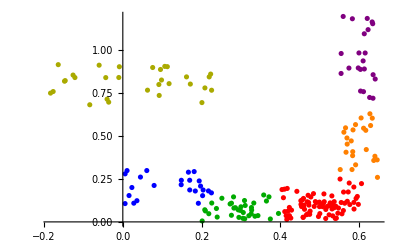

```mathematica
ListPlot[Ex4ClusteringsAlpha⟦5⟧,PlotStyle->{Blue,Red,Darker[Green],Orange,Purple,Darker[Yellow],Gray}⟦1;;6⟧]
```

## Exemplo 5: Avaliação paramétrica no espaço de taxas de mutação e tamanho da população num algoritmo genético

```mathematica
Ex5cidades=Table[{10*RandomReal[],10*RandomReal[]},{10}]
```

{{1.35811,3.2238},{9.61761,9.87567},{9.20995,5.60758},{2.28885,9.28101},{7.12989,4.70045},{5.87883,0.848145},{7.94194,5.70085},{5.26195,4.11173},{1.34671,2.73954},{4.56436,9.22432}}

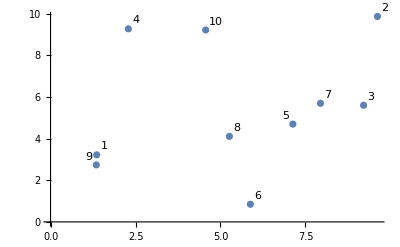

```mathematica
ListPlot[Labeled[#⟦1⟧,#⟦2⟧]&/@MapThread[List,{Ex5cidades,Range[1,10]}]]
```

```mathematica
Ex5matrizdistancias=Table[N[EuclideanDistance[Ex5cidades⟦i⟧,Ex5cidades⟦j⟧],4],{i,1,10},{j,1,10}];
MatrixForm[Ex5matrizdistancias]
```

(0. | 10.605 | 8.20571 | 6.1283 | 5.95767 | 5.10692 | 7.03438 | 4.00354 | 0.484391 | 6.8034
10.605 | 0. | 4.28752 | 7.35285 | 5.7421 | 9.77112 | 4.49856 | 7.2246 | 10.9239 | 5.09506
8.20571 | 4.28752 | 0. | 7.83554 | 2.26926 | 5.80935 | 1.27144 | 4.22188 | 8.36995 | 5.88747
6.1283 | 7.35285 | 7.83554 | 0. | 6.66462 | 9.16522 | 6.69141 | 5.96329 | 6.60896 | 2.27622
5.95767 | 5.7421 | 2.26926 | 6.66462 | 0. | 4.05036 | 1.2885 | 1.95852 | 6.10657 | 5.2007
5.10692 | 9.77112 | 5.80935 | 9.16522 | 4.05036 | 0. | 5.27306 | 3.32138 | 4.91096 | 8.47869
7.03438 | 4.49856 | 1.27144 | 6.69141 | 1.2885 | 5.27306 | 0. | 3.11571 | 7.22955 | 4.88087
4.00354 | 7.2246 | 4.22188 | 5.96329 | 1.95852 | 3.32138 | 3.11571 | 0. | 4.14873 | 5.15996
0.484391 | 10.9239 | 8.36995 | 6.60896 | 6.10657 | 4.91096 | 7.22955 | 4.14873 | 0. | 7.23917
6.8034 | 5.09506 | 5.88747 | 2.27622 | 5.2007 | 8.47869 | 4.88087 | 5.15996 | 7.23917 | 0.)

```mathematica
Ex5DrawRoute[rota_,fitness_]:=Labeled[Graph[Range[1,10],Join[Table[rota⟦i⟧->rota⟦i+1⟧,{i,1,9}],{rota⟦10⟧->rota⟦1⟧}],VertexCoordinates->Ex5cidades,VertexLabels->"Name"],1/fitness];
```

```mathematica
Ex5ComprimentoRota[rota_]:=Total[Table[Ex5matrizdistancias⟦rota⟦i⟧,rota⟦i+1⟧⟧,{i,1,9}]]+Ex5matrizdistancias⟦rota⟦10⟧,rota⟦1⟧⟧;
```

```mathematica
Ex5Fitness[x_]:=1/Ex5ComprimentoRota[x];
```

```mathematica
Ex5OrderedReplace[p1_List,p2_List,range_List]:=ReplacePart[p2/.MapThread[Rule,{Complement[Range[1,10],p2⟦#⟧&/@range],Complement[Range[1,10],p1⟦#⟧&/@range]}],MapThread[Rule,{range,p1⟦#⟧&/@range}]];
```

```mathematica
Ex5Crossover[x_,y_]:=With[{range=Range[Min[#],Max[#]]&@{RandomInteger[{1,10}],RandomInteger[{1,10}]}},{Ex5OrderedReplace[x,y,range],Ex5OrderedReplace[y,x,range]}];
Ex5Crossover[pop_]:=Flatten[Ex5Crossover[#⟦1⟧,#⟦2⟧]&/@Partition[pop,2],1];
```

```mathematica
Ex5Mutation[pop_,pm_]:=Table[If[RandomReal[]≤pm,With[{parts=RandomSample[Range[1,10],2]},ReplacePart[x,{parts⟦1⟧->x⟦parts⟦2⟧⟧,parts⟦2⟧->x⟦parts⟦1⟧⟧}]],x],{x,pop}];
```

#### Busca no espaço de taxas de mutação e tamanho da população

```mathematica
Ex5PopSizes=Range[50,150,10]
Ex5InitialPopulations=Table[Table[RandomSample[Range[1,10],10],{size}],{size,Ex5PopSizes}];
```

{50,60,70,80,90,100,110,120,130,140,150}

```mathematica
Ex5pms=Range[0.0,0.3,0.05]
Ex5maxit=50;
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3}

```mathematica
Ex5Run=Table[{"Pop. Size = "<>ToString[Ex5PopSizes⟦i⟧],"Mutation rate = "<>ToString[m],AG[Ex5InitialPopulations⟦i⟧,Ex5Fitness,Ex5Crossover,Ex5Mutation,m,Ex5maxit,Infinity,All,False]⟦2⟧},{i,1,Length@Ex5PopSizes},{m,Ex5pms}];
```

```mathematica
MatrixForm[SortBy[Flatten[Ex5Run,1],(-Last[#])&]]
```

(Pop. Size = 110 | Mutation rate = 0.15 | 0.0322349
Pop. Size = 110 | Mutation rate = 0.2 | 0.0322349
Pop. Size = 70 | Mutation rate = 0.2 | 0.0310423
Pop. Size = 80 | Mutation rate = 0.05 | 0.0309101
Pop. Size = 80 | Mutation rate = 0.15 | 0.029781
Pop. Size = 140 | Mutation rate = 0.05 | 0.0294506
Pop. Size = 120 | Mutation rate = 0.3 | 0.0289901
Pop. Size = 70 | Mutation rate = 0.3 | 0.0287841
Pop. Size = 120 | Mutation rate = 0.05 | 0.0285042
Pop. Size = 90 | Mutation rate = 0. | 0.0285042
Pop. Size = 100 | Mutation rate = 0.15 | 0.0283594
Pop. Size = 50 | Mutation rate = 0.2 | 0.0283355
Pop. Size = 110 | Mutation rate = 0.05 | 0.0283213
Pop. Size = 80 | Mutation rate = 0.3 | 0.0281118
Pop. Size = 80 | Mutation rate = 0.25 | 0.0277406
Pop. Size = 120 | Mutation rate = 0.25 | 0.027655
Pop. Size = 150 | Mutation rate = 0.15 | 0.0275137
Pop. Size = 110 | Mutation rate = 0.3 | 0.0274777
Pop. Size = 130 | Mutation rate = 0. | 0.0274369
Pop. Size = 90 | Mutation rate = 0.25 | 0.0273216
Pop. Size = 120 | Mutation rate = 0.15 | 0.0271982
Pop. Size = 60 | Mutation rate = 0.3 | 0.0271722
Pop. Size = 120 | Mutation rate = 0.1 | 0.0271699
Pop. Size = 100 | Mutation rate = 0. | 0.0270609
Pop. Size = 150 | Mutation rate = 0.1 | 0.0268953
Pop. Size = 130 | Mutation rate = 0.2 | 0.0267068
Pop. Size = 130 | Mutation rate = 0.1 | 0.0266922
Pop. Size = 60 | Mutation rate = 0. | 0.0266655
Pop. Size = 140 | Mutation rate = 0.25 | 0.0266646
Pop. Size = 60 | Mutation rate = 0.05 | 0.0266021
Pop. Size = 80 | Mutation rate = 0. | 0.026526
Pop. Size = 60 | Mutation rate = 0.15 | 0.0264579
Pop. Size = 150 | Mutation rate = 0.25 | 0.0262335
Pop. Size = 130 | Mutation rate = 0.15 | 0.0261564
Pop. Size = 100 | Mutation rate = 0.3 | 0.0261508
Pop. Size = 140 | Mutation rate = 0. | 0.0261486
Pop. Size = 140 | Mutation rate = 0.1 | 0.0259948
Pop. Size = 150 | Mutation rate = 0.05 | 0.0259647
Pop. Size = 130 | Mutation rate = 0.05 | 0.0259267
Pop. Size = 100 | Mutation rate = 0.2 | 0.0257284
Pop. Size = 80 | Mutation rate = 0.1 | 0.0257284
Pop. Size = 50 | Mutation rate = 0. | 0.0257177
Pop. Size = 50 | Mutation rate = 0.3 | 0.0256765
Pop. Size = 50 | Mutation rate = 0.1 | 0.0256577
Pop. Size = 100 | Mutation rate = 0.25 | 0.0255941
Pop. Size = 140 | Mutation rate = 0.2 | 0.0255782
Pop. Size = 100 | Mutation rate = 0.05 | 0.0255562
Pop. Size = 70 | Mutation rate = 0.1 | 0.0255283
Pop. Size = 110 | Mutation rate = 0.1 | 0.025527
Pop. Size = 110 | Mutation rate = 0.25 | 0.0254526
Pop. Size = 70 | Mutation rate = 0.25 | 0.0254382
Pop. Size = 150 | Mutation rate = 0.2 | 0.0254277
Pop. Size = 90 | Mutation rate = 0.05 | 0.025406
Pop. Size = 130 | Mutation rate = 0.25 | 0.025404
Pop. Size = 70 | Mutation rate = 0.05 | 0.025404
Pop. Size = 110 | Mutation rate = 0. | 0.0252796
Pop. Size = 80 | Mutation rate = 0.2 | 0.0251989
Pop. Size = 90 | Mutation rate = 0.15 | 0.025167
Pop. Size = 140 | Mutation rate = 0.3 | 0.0251227
Pop. Size = 150 | Mutation rate = 0.3 | 0.0250103
Pop. Size = 50 | Mutation rate = 0.25 | 0.0249271
Pop. Size = 120 | Mutation rate = 0. | 0.0249245
Pop. Size = 70 | Mutation rate = 0. | 0.0248682
Pop. Size = 50 | Mutation rate = 0.05 | 0.0248342
Pop. Size = 130 | Mutation rate = 0.3 | 0.0247303
Pop. Size = 120 | Mutation rate = 0.2 | 0.0245952
Pop. Size = 150 | Mutation rate = 0. | 0.0245445
Pop. Size = 70 | Mutation rate = 0.15 | 0.0243155
Pop. Size = 90 | Mutation rate = 0.1 | 0.0241396
Pop. Size = 90 | Mutation rate = 0.3 | 0.0240911
Pop. Size = 60 | Mutation rate = 0.25 | 0.0238211
Pop. Size = 60 | Mutation rate = 0.2 | 0.0236956
Pop. Size = 90 | Mutation rate = 0.2 | 0.0234342
Pop. Size = 60 | Mutation rate = 0.1 | 0.0234287
Pop. Size = 100 | Mutation rate = 0.1 | 0.023413
Pop. Size = 50 | Mutation rate = 0.15 | 0.0224765
Pop. Size = 140 | Mutation rate = 0.15 | 0.0224632)

#### Uma vez encontrado o melhor conjunto de parâmetros, investigar a média e o desvio-padrão num conjunto de 100 execuções.

```mathematica
Ex5BestPopSize=110;
Ex5BestMutationRate=0.15;
```

```mathematica
Ex5BestRuns=Table[AG[Table[RandomSample[Range[1,10],10],{Ex5BestPopSize}],Ex5Fitness,Ex5Crossover,Ex5Mutation,Ex5BestMutationRate,Ex5maxit,Infinity,All,False]⟦2⟧,{100}];
```

```mathematica
Ex5BestStatistics={Mean[Ex5BestRuns],StandardDeviation[Ex5BestRuns]}
```

{0.0264715,0.00213618}

```mathematica
Ex5BestDistanceStatistics={Mean[1/Ex5BestRuns],StandardDeviation[1/Ex5BestRuns]}
```

{38.0071,2.90261}

### Análise do desempenho do melhor conjunto de parâmetros em relação a quantidade máxima de iterações

```mathematica
Ex5MaxIts=Range[50,200,10]
```

{50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200}

```mathematica
Ex5MaxItAnalysis=Table[AG[Table[RandomSample[Range[1,10],10],{Ex5BestPopSize}],Ex5Fitness,Ex5Crossover,Ex5Mutation,Ex5BestMutationRate,maxit,Infinity,All,False]⟦2⟧,{maxit,Ex5MaxIts}];
```

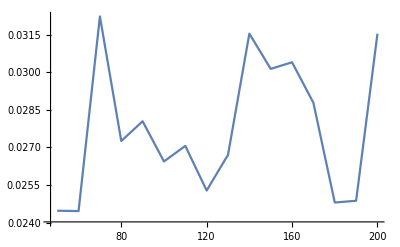

```mathematica
ListLinePlot[Ex5MaxItAnalysis,DataRange->{50,200}]
```

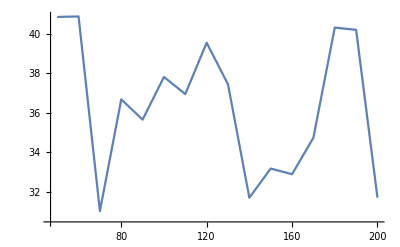

```mathematica
ListLinePlot[1/Ex5MaxItAnalysis,DataRange->{50,200}]
```

```mathematica
Ex5BestMaxIt=70;
```

```mathematica
Ex5BestMaxItRuns=Table[AG[Table[RandomSample[Range[1,10],10],{Ex5BestPopSize}],Ex5Fitness,Ex5Crossover,Ex5Mutation,Ex5BestMutationRate,Ex5BestMaxIt,Infinity,All,False]⟦2⟧,{100}];
```

```mathematica
{Mean[Ex5BestMaxItRuns],StandardDeviation[Ex5BestMaxItRuns]}
```

{0.0269361,0.00208937}

```mathematica
{Mean[1/Ex5BestMaxItRuns],StandardDeviation[1/Ex5BestMaxItRuns]}
```

{37.3387,2.79685}